1/2

0.001

0.1

0.25 (-3-ⅇ^(-0.2 t)+4 ⅇ^(-0.1 t)+0.2 t)

1

0.001

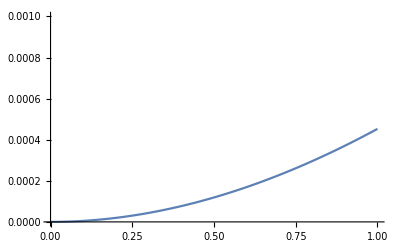

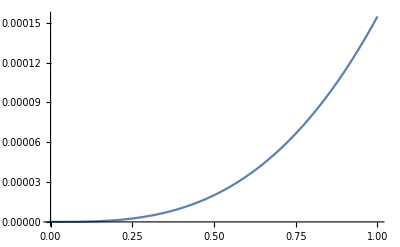

```mathematica
vo = 5 10^-4/10^-3
d = 0.001
α = 0.1
β[t_]=(vo^2 d)/α^3(2 α t - Exp[-2 α t] + 4 Exp[-α t]-3)
xmax = 1
ymax = 0.001
(*Plot[β[t],{t,0,xmax},PlotRange->{{0,xmax},{0,ymax}}]*)
Plot[Evaluate[D[β[t],t]],{t,0,xmax},PlotRange->{{0,xmax},{0,ymax}}]
Plot[β[t],{t,0,xmax},PlotRange->All]
```

```mathematica
thetCorr[s_,t_]= df/αf(Exp[-αf (t-s)]-Exp[-αf (t+s)])
yThetCorr = vof Integrate[thetCorr[s,t],{s,0,t}]//Expand
betF = 2vof Integrate[yThetCorr,{t,0,T}]
```

(df (ⅇ^(-((-s+t) αf))-ⅇ^(-((s+t) αf))))/αf

(df vof)/αf^2+(df ⅇ^(-2 t αf) vof)/αf^2-(2 df ⅇ^(-t αf) vof)/αf^2

-(df vof^2 (3+ⅇ^(-2 T αf)-4 ⅇ^(-T αf)-2 T αf))/αf^3

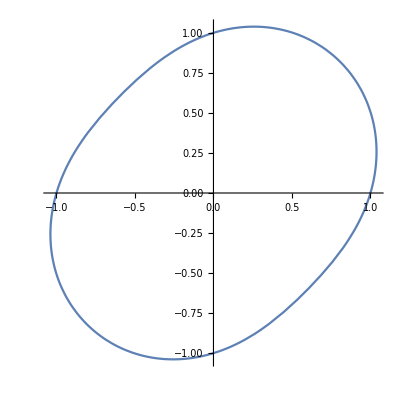

```mathematica
ρ[s_]:=1+0.15 Sin[4π s]
x[s_]:= ρ[s]Cos[2π s]
y[s_]:= ρ[s]Sin[2π s]
ParametricPlot[{x[s],y[s]}, {s,0,1},PlotRange->All]
```

```mathematica
Clear[{ρ,x,y}]
ρ[s_]:=1+λ Sin[n 2π s]
x[s_]:= ρ[s]Cos[2π s]
y[s_]:= ρ[s]Sin[2π s]
```

```mathematica
tx[s_]=D[x[s],s] 
ty[s_]=D[y[s],s] 
tHat[s_]={tx[s]/(tx[s]^2+ty[s]^2),ty[s]/(tx[s]^2+ty[s]^2)}//FullSimplify
```

```mathematica
f[ϕ_]:=ArcTan[ϕ]
Series[f[ϕ+δϕ],{δϕ,0,2}]
```

ArcTan[ϕ]+δϕ/(1+ϕ^2)-(ϕ δϕ^2)/((1+ϕ^2)^2)+O[δϕ]^3

```mathematica
Integrate[ Exp[-I (k-l) x],{x,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^(-ⅈ (k-l) x) does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(-ⅈ (k-l) x)ⅆx

```mathematica
FourierTransform[DiracDelta[x],x,k]
```

1/(√(2 π))

```mathematica
Integrate[Sin [(m π s)/l]Sin [(m π s)/l],{s,0,l}]
```

1/4 l (2-Sin[2 m π]/(m π))

```mathematica
Integrate[Exp[-α a^2],{a,-∞,∞}]
```

ConditionalExpression[(√π)/(√α), Re[α]>0]

```mathematica
Integrate[Exp[-ko τ+ ah Exp[I 2 π k τ/l]],{τ,s,l}]
```

∫_s^l ⅇ^(ah ⅇ^((2 ⅈ k π τ)/l)-ko τ)ⅆτ

```mathematica
vint[ϕst_,ko_, s_, sc_]:=ϕst/ko(Exp[-ko s/ϕst]-Exp[-ko sc/ϕst])
ψ[s_,sc_,vo_,d_,ν_]:=(vo^2 d)/ν((2 ν (s-sc))/vo - Exp[-2ν(s-sc)/vo]+4Exp[-ν(s-sc)/vo]-3)
vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]:= (σ μ)/ψ[s,sc,vo,d,ν]
vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_] := vint[ϕst,ko, 0, sc]+vOU[sSt,sc,vo,d,ν, σ, μ]
```

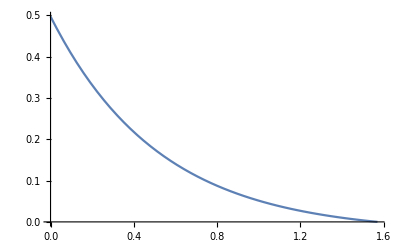

```mathematica
scV = π/2;
Plot[vint[π/6,1,s,scV],{s,0,scV},PlotRange->All]
```

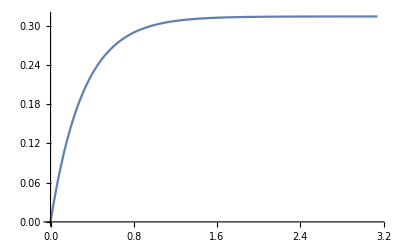

```mathematica
Plot[vint[π/10,1,0,sc],{sc,0,π},PlotRange->All]
```

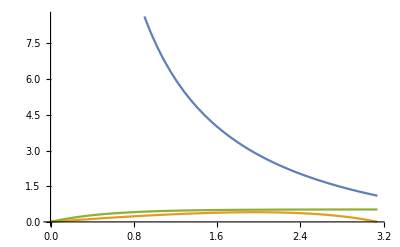

```mathematica
Plot[{ψ[2π,sc,1,sc^-1,1],vOU[2π,sc,1,sc^-1,1, 1, π-sc],vint[π/6,1,0,sc]},{sc,0,π},PlotRange->Automatic]
```

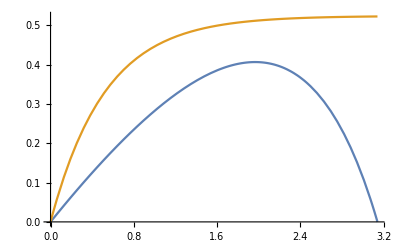

```mathematica
Plot[{vOU[2π,sc,1,sc^-1,1, 1,π-sc],vint[π/6,1,0,sc]},{sc,0,π},PlotRange->Automatic]
```

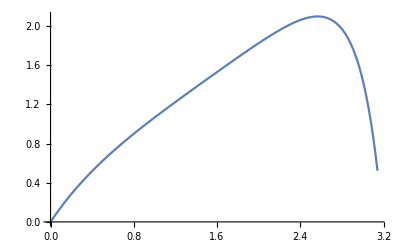

```mathematica
Plot[{vOU[π+1,sc,1,sc^-1,1, 1,π-sc]+vint[π/6,1,0,sc]},{sc,0,π},PlotRange->Automatic]
```

```mathematica
D[expr,sc]==0
```

ⅇ^(-(ko sc)/ϕst)-(μ ν (-(2 ν)/vo-(2 ⅇ^(-(2 (-sc+sSt) ν)/vo) ν)/vo+(4 ⅇ^(-((-sc+sSt) ν)/vo) ν)/vo) σ)/(d vo^2 (-3-ⅇ^(-(2 (-sc+sSt) ν)/vo)+4 ⅇ^(-((-sc+sSt) ν)/vo)+(2 (-sc+sSt) ν)/vo)^2)==0

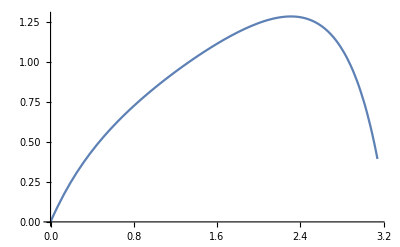

```mathematica
(*vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_] *)
Plot[vFull[3π/2, sc,1,sc^-1,1,1,π-sc,π/8,1],{sc,0,π},PlotRange->Automatic]
```